```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

Gaussian fidelities from energy calc (more x steps)
sumterms = 4

```mathematica
STAlist={{1.,0.7401869},{1.25,0.7783941},{1.5,0.807918},{1.75,0.8314413},{2.,0.8506148},{2.25,0.8665222},{2.5,0.8799097},{2.75,0.8913104},{3.,0.9011167},{3.25,0.9096243},{3.5,0.9170605},{3.75,0.9236033},{4.,0.9293938},{4.25,0.9345457},{4.5,0.9391513},{4.75,0.9432863},{5.,0.9470136},{5.25,0.9503858},{5.5,0.9534469},{5.75,0.9562343},{6.,0.9587799},{6.25,0.961111},{6.5,0.9632511},{6.75,0.9652206},{7.,0.9670371},{7.5,0.970271},{8.,0.973055},{8.5,0.9754686},{9.,0.9775744},{9.5,0.9794223},{10.,0.9810523},{10.5,0.9824973},{11.,0.9837839},{11.5,0.9849343},{12.,0.9859669},{12.5,0.9868971},{13.,0.9877378},{13.5,0.9885001},{14.,0.9891934},{14.5,0.9898258},{15.,0.990404},{15.5,0.9909341},{16.,0.9914212}};
eSTA1storder1comp={{1.,0.5398342},{1.25,0.6739242},{1.5,0.7595637},{1.75,0.8161262},{2.,0.8550192},{2.25,0.8827699},{2.5,0.9032146},{2.75,0.9186938},{3.,0.9306903},{3.25,0.9401754},{3.5,0.9478057},{3.75,0.9540369},{4.,0.9591931},{4.25,0.9635096},{4.5,0.9671606},{4.75,0.9702774},{5.,0.9729601},{5.25,0.9752865},{5.5,0.9773176},{5.75,0.9791018},{6.,0.9806779},{6.25,0.9820775},{6.5,0.9833262},{6.75,0.9844451},{7.,0.9854518},{7.5,0.987185},{8.,0.9886176},{8.5,0.989816},{9.,0.9908291},{9.5,0.9916935},{10.,0.9924373},{10.5,0.993082},{11.,0.9936446},{11.5,0.9941385},{12.,0.9945744},{12.5,0.9949609},{13.,0.9953054},{13.5,0.9956137},{14.,0.9958906},{14.5,0.9961404},{15.,0.9963667},{15.5,0.9965723},{16.,0.9967598}};
eSTA2ndorder1comp={{1.,0.7855974},{1.25,0.8514373},{1.5,0.8899133},{1.75,0.9144087},{2.,0.9310522},{2.25,0.9429431},{2.5,0.9517814},{2.75,0.9585623},{3.,0.9639011},{3.25,0.9681954},{3.5,0.971712},{3.75,0.974636},{4.,0.977099},{4.25,0.9791974},{4.5,0.9810027},{4.75,0.9825694},{5.,0.9839394},{5.25,0.9851456},{5.5,0.9862143},{5.75,0.9871661},{6.,0.9880183},{6.25,0.9887847},{6.5,0.9894768},{6.75,0.9901041},{7.,0.9906749},{7.5,0.9916726},{8.,0.9925131},{8.5,0.9932284},{9.,0.9938427},{9.5,0.9943743},{10.,0.9948376},{10.5,0.995244},{11.,0.9956025},{11.5,0.9959204},{12.,0.9962037},{12.5,0.9964574},{13.,0.9966853},{13.5,0.996891},{14.,0.9970773},{14.5,0.9972465},{15.,0.9974008},{15.5,0.9975417},{16.,0.9976709}};
eSTA1storder8comp={{1.,0.5263606},{1.25,0.663318},{1.5,0.7513195},{1.75,0.8096326},{2.,0.8498108},{2.25,0.8785187},{2.5,0.8996906},{2.75,0.9157338},{3.,0.928176},{3.25,0.9380196},{3.5,0.9459426},{3.75,0.9524161},{4.,0.9577752},{4.25,0.9622635},{4.5,0.9660613},{4.75,0.9693045},{5.,0.9720969},{5.25,0.9745192},{5.5,0.9766344},{5.75,0.978493},{6.,0.980135},{6.25,0.9815933},{6.5,0.9828944},{6.75,0.9840603},{7.,0.9851092},{7.5,0.9869149},{8.,0.9884069},{8.5,0.9896542},{9.,0.9907079},{9.5,0.9916062},{10.,0.9923784},{10.5,0.9930471},{11.,0.9936299},{11.5,0.994141},{12.,0.9945916},{12.5,0.9949909},{13.,0.9953463},{13.5,0.995664},{14.,0.9959493},{14.5,0.9962064},{15.,0.996439},{15.5,0.9966503},{16.,0.9968429}};
eSTA2ndorder8comp={{1.,0.7820503},{1.25,0.8487124},{1.5,0.8877195},{1.75,0.9125827},{2.,0.9294965},{2.25,0.9415956},{2.5,0.9506003},{2.75,0.957518},{3.,0.9629719},{3.25,0.9673647},{3.5,0.9709668},{3.75,0.9739657},{4.,0.9764951},{4.25,0.9786525},{4.5,0.9805109},{4.75,0.9821253},{5.,0.9835385},{5.25,0.984784},{5.5,0.9858883},{5.75,0.9868727},{6.,0.9877546},{6.25,0.9885482},{6.5,0.9892652},{6.75,0.9899154},{7.,0.9905072},{7.5,0.9915418},{8.,0.9924136},{8.5,0.9931553},{9.,0.9937919},{9.5,0.9943424},{10.,0.9948218},{10.5,0.9952418},{11.,0.9956118},{11.5,0.9959396},{12.,0.9962313},{12.5,0.9964921},{13.,0.9967263},{13.5,0.9969374},{14.,0.9971283},{14.5,0.9973017},{15.,0.9974596},{15.5,0.9976038},{16.,0.9977359}};
```

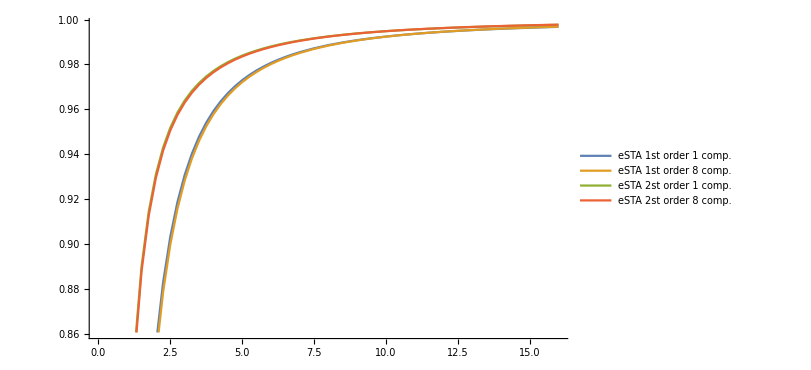

```mathematica
ListLinePlot[{eSTA1storder1comp,eSTA1storder8comp,eSTA2ndorder1comp,eSTA2ndorder8comp},PlotLegends->{"eSTA 1st order 1 comp.","eSTA 1st order 8 comp.","eSTA 2st order 1 comp.","eSTA 2st order 8 comp."}
,ImageSize->600]
```

Gaussian plot

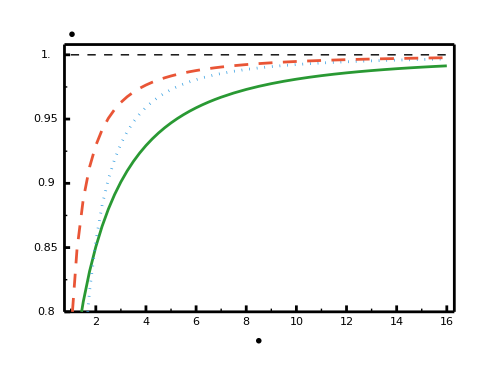

```mathematica
classColour=RGBColor[1, 0, 0];
minAnharmColour=RGBColor[0, 0.6, 0];
polyColour=RGBColor[0, 0, 0.6];

classColour=RGBColor[0.915, 0.3325, 0.2125];
minAnharmColour=RGBColor[0.16, 0.6, 0.2];
polyColour=RGBColor[0.16, 0.6, 0.88];

(*** Plot window ***)
xMin=1.0;xMax=16.0;
yMin=0.8;yMax=1.0;
(*** Frame window offsets ***)
xoffset=0.25;
yoffset=0.008;
xoffsetRight=0.3;

aspectRatio=0.75;
imageSize=500;

fontSize=18;
matexMag=2;
gridThickness=0.0001;

axesThickness=0.004;
plotThickness=0.004;

tickMajorThickness=0.004;
tickMinorThickness=tickMajorThickness/2;

yLabelOffset=0.03;
yLabelSteps=0.1;
yTickMajorList=Table[i,{i,0.8,1.0,0.05}];
ytickMajorLength=0.225;
yTickMinorList=Table[i,{i,0.825,0.975,0.025}];
ytickMinorLength=ytickMajorLength/2;

xTickMajorList=Table[i,{i,2.0,16.0,2}];
xtickMajorHeight=0.005;
xTickMinorList=Table[i,{i,1,15,2}];
xtickMinorHeight=xtickMajorHeight/2;
xLabelSteps=Length[xTickMajorList];

lighterVal=0.0;
dVal=0.5;

numSum=4;
plotOutputsinSq=
ListLinePlot[{
STAlist
,
eSTA1storder1comp
,
eSTA2ndorder8comp
(*,
eSTA1storder1comp
,
eSTA2ndorder8comp*)
}
,PlotRange->{{xMin,xMax},{yMin,yMax}}
,PlotStyle->{
{minAnharmColour, Thickness[plotThickness]}
(*,{polyColour,Thickness[plotThickness]}
,{classColour,Thickness[plotThickness]}*)
,{polyColour, Thickness[plotThickness],Dotted}
,{classColour,Thickness[plotThickness],Dashing[{0.02,0.015}]}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,Frame->False
,Axes->False
];

frame=Graphics[{
(*** Dashed F=1 Line ***)
{
{AbsoluteDashing[6],Line[{{xMin,1},{xMax,1}}]}
}
,
(*** Frame ***)
{
Thickness[axesThickness]
,Line[{{xMin-xoffset,yMin},{xMax+xoffsetRight,yMin}}]
,Line[{{xMax+xoffsetRight,yMin},{xMax+xoffsetRight,yMax+yoffset}}]
,Line[{{xMax+xoffsetRight,yMax+yoffset},{xMin-xoffset,yMax+yoffset}}]
,Line[{{xMin-xoffset,yMax+yoffset},{xMin-xoffset,yMin}}]
}
,
{
(*** Ticks Major ***)
Thickness[tickMajorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMajorHeight}}],{i,xTickMajorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMajorLength,i}}],{i,yTickMajorList}]
}
,
{
(*** Ticks Minor ***)
Thickness[tickMinorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMinorHeight}}],{i,xTickMinorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMinorLength,i}}],{i,yTickMinorList}]
}
,
{
(*** Tick Major values ***)
(* x-axis *)Table[Inset[Round@i,{i,yMin-0.008}],{i,xTickMajorList}]
,
(* y-axis *)Table[Inset[i,{xMin-1,i}],{i,yTickMajorList}]
}
,
{
(*** Axes labels ***)
(* x-axis *)Inset[MaTeX["\\tau_G",Magnification->matexMag],{(1.xMax-xMin)/2+xMin,yMin-0.0225}]
,
(* y-axis *)Inset[MaTeX["F",Magnification->matexMag],{xMin+0.05,yMax+0.016}]
}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,LabelStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman",Black}
,AspectRatio->aspectRatio
,ImageSize->imageSize];

mainPlotsinSq0=Show[frame,plotOutputsinSq]
```

Fidelity landscape 1 comps

```mathematica
lambdas[4][1]=Import["./delta_lambdas/1_particle_opening_exp_U0=2417.82_Tf=1._to_16._numSumTerms=4_numComps=1_eSTA0_Tfover2.dat"]
```

{{1.,0.194131},{1.25,0.124262},{1.5,0.0863089},{1.75,0.063424},{2.,0.0485707},{2.25,0.0383871},{2.5,0.0311027},{2.75,0.0257129},{3.,0.0216134},{3.25,0.0184229},{3.5,0.0158912},{3.75,0.0138486},{4.,0.0121768},{4.25,0.0107912},{4.5,0.00962995},{4.75,0.0086471},{5.,0.00780789},{5.25,0.00708563},{5.5,0.00645955},{5.75,0.00591329},{6.,0.00543384},{6.25,0.00501071},{6.5,0.00463543},{6.75,0.00430102},{7.,0.00400177},{7.5,0.00349043},{8.,0.0030718},{8.5,0.00272473},{9.,0.00243374},{9.5,0.00218737},{10.,0.0019769},{10.5,0.00179569},{11.,0.00163855},{11.5,0.00150139},{12.,0.00138098},{12.5,0.0012747},{13.,0.00118043},{13.5,0.00109643},{14.,0.00102127},{14.5,0.000953726},{15.,0.000892806},{15.5,0.000837658},{16.,0.000787562}}

```mathematica
lambdas[4][1]={{1.,0.19413062388464852},{1.25,0.1242622406527385},{1.5,0.08630886914182606},{1.75,0.063424007238442},{2.,0.04857067866366849},{2.25,0.03838711775646488},{2.5,0.031102715861947683},{2.75,0.025712929964452926},{3.,0.021613412765741778},{3.25,0.018422891307062657},{3.5,0.01589118728786399},{3.75,0.013848624994617382},{4.,0.012176834783105937},{4.25,0.01079120295745988},{4.5,0.009629946093533976},{4.75,0.008647098937202816},{5.,0.007807892066958387},{5.25,0.007085631906244438},{5.5,0.0064595498952433085},{5.75,0.005913291445426659},{6.,0.005433836086439447},{6.25,0.005010713718063615},{6.5,0.004635427691246267},{6.75,0.004301024619721194},{7.,0.004001769777750712},{7.5,0.003490430245060782},{8.,0.003071803538461325},{8.5,0.0027247255789775776},{9.,0.002433744101807256},{9.5,0.002187366489950019},{10.,0.001976904097960498},{10.5,0.00179569130339676},{11.,0.0016385462026154635},{11.5,0.0015013909056541966},{12.,0.001380979616851144},{12.5,0.001274701046385805},{13.,0.0011804330856050138},{13.5,0.0010964348727004716},{14.,0.0010212659942344933},{14.5,0.0009537255837790246},{15.,0.0008928060874750911},{15.5,0.0008376578405941067},{16.,0.0007875615738439406}};
```

```mathematica
(* pps = 512 *)
boxSearchList512=Import["./Global_Output/U0t_open_exp_U0=2417.82_L=200_gamma=10_sumTerms=4_numComps=1_eSTA_box_search/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_parabola.dat"];
```

```mathematica
boxSearchList512={{13.,0.9771536,0,0},{13.,0.9784375,1,0},{13.,0.9796821,2,0},{13.,0.9808867,3,0},{13.,0.9820511,4,0},{13.,0.9831747,5,0},{13.,0.9842571,6,0},{13.,0.9852978,7,0},{13.,0.9862964,8,0},{13.,0.9872526,9,0},{13.,0.9881659,10,0},{13.,0.9890359,11,0},{13.,0.9898622,12,0},{13.,0.9906445,13,0},{13.,0.9913823,14,0},{13.,0.9920755,15,0},{13.,0.9927235,16,0},{13.,0.9933262,17,0},{13.,0.9938831,18,0},{13.,0.9943941,19,0},{13.,0.9948587,20,0},{13.,0.9952768,21,0},{13.,0.9956481,22,0},{13.,0.9959724,23,0},{13.,0.9962494,24,0},{13.,0.996479,25,0},{13.,0.9966609,26,0},{13.,0.996795,27,0},{13.,0.9968811,28,0},{13.,0.9969191,29,0},{13.,0.9969089,30,0},{13.,0.9968503,31,0},{13.,0.9967433,32,0},{13.,0.9965878,33,0},{13.,0.9963838,34,0},{13.,0.9961312,35,0},{13.,0.9958299,36,0},{13.,0.9954801,37,0},{13.,0.9950817,38,0},{13.,0.9946347,39,0},{13.,0.9941393,40,0},{13.,0.9935955,41,0},{13.,0.9930034,42,0},{13.,0.992363,43,0},{13.,0.9916747,44,0},{13.,0.9909384,45,0},{13.,0.9901544,46,0},{13.,0.9893229,47,0},{13.,0.988444,48,0},{13.,0.9875181,49,0},{13.,0.9865453,50,0},{13.5,0.9785711,0,0},{13.5,0.9797768,1,0},{13.5,0.9809453,2,0},{13.5,0.982076,3,0},{13.5,0.9831687,4,0},{13.5,0.9842229,5,0},{13.5,0.9852383,6,0},{13.5,0.9862144,7,0},{13.5,0.9871509,8,0},{13.5,0.9880474,9,0},{13.5,0.9889035,10,0},{13.5,0.989719,11,0},{13.5,0.9904934,12,0},{13.5,0.9912265,13,0},{13.5,0.9919179,14,0},{13.5,0.9925674,15,0},{13.5,0.9931747,16,0},{13.5,0.9937394,17,0},{13.5,0.9942613,18,0},{13.5,0.9947402,19,0},{13.5,0.9951758,20,0},{13.5,0.9955678,21,0},{13.5,0.9959162,22,0},{13.5,0.9962205,23,0},{13.5,0.9964808,24,0},{13.5,0.9966968,25,0},{13.5,0.9968683,26,0},{13.5,0.9969952,27,0},{13.5,0.9970773,28,0},{13.5,0.9971146,29,0},{13.5,0.9971069,30,0},{13.5,0.9970542,31,0},{13.5,0.9969563,32,0},{13.5,0.9968133,33,0},{13.5,0.996625,34,0},{13.5,0.9963915,35,0},{13.5,0.9961128,36,0},{13.5,0.9957888,37,0},{13.5,0.9954195,38,0},{13.5,0.9950051,39,0},{13.5,0.9945456,40,0},{13.5,0.994041,41,0},{13.5,0.9934914,42,0},{13.5,0.9928969,43,0},{13.5,0.9922577,44,0},{13.5,0.9915739,45,0},{13.5,0.9908456,46,0},{13.5,0.9900731,47,0},{13.5,0.9892564,48,0},{13.5,0.9883959,49,0},{13.5,0.9874917,50,0},{14.,0.9798602,0,0},{14.,0.9809946,1,0},{14.,0.9820938,2,0},{14.,0.9831572,3,0},{14.,0.9841847,4,0},{14.,0.9851758,5,0},{14.,0.9861301,6,0},{14.,0.9870474,7,0},{14.,0.9879274,8,0},{14.,0.9887696,9,0},{14.,0.9895739,10,0},{14.,0.9903398,11,0},{14.,0.9910671,12,0},{14.,0.9917556,13,0},{14.,0.9924049,14,0},{14.,0.9930147,15,0},{14.,0.9935849,16,0},{14.,0.9941152,17,0},{14.,0.9946053,18,0},{14.,0.995055,19,0},{14.,0.9954642,20,0},{14.,0.9958326,21,0},{14.,0.99616,22,0},{14.,0.9964462,23,0},{14.,0.9966912,24,0},{14.,0.9968947,25,0},{14.,0.9970566,26,0},{14.,0.9971768,27,0},{14.,0.9972552,28,0},{14.,0.9972916,29,0},{14.,0.997286,30,0},{14.,0.9972384,31,0},{14.,0.9971485,32,0},{14.,0.9970165,33,0},{14.,0.9968422,34,0}};
```

```mathematica
realFidLand512=Table[{-0.5+0.05*boxSearchList512[[j,3]],boxSearchList512[[j,2]]},{j,1,51}]
```

```mathematica
realFidLand512={{-0.5,0.9771536},{-0.45,0.9784375},{-0.4,0.9796821},{-0.35,0.9808867},{-0.3,0.9820511},{-0.25,0.9831747},{-0.19999999999999996,0.9842571},{-0.14999999999999997,0.9852978},{-0.09999999999999998,0.9862964},{-0.04999999999999999,0.9872526},{0.,0.9881659},{0.050000000000000044,0.9890359},{0.10000000000000009,0.9898622},{0.15000000000000002,0.9906445},{0.20000000000000007,0.9913823},{0.25,0.9920755},{0.30000000000000004,0.9927235},{0.3500000000000001,0.9933262},{0.4,0.9938831},{0.45000000000000007,0.9943941},{0.5,0.9948587},{0.55,0.9952768},{0.6000000000000001,0.9956481},{0.6500000000000001,0.9959724},{0.7000000000000002,0.9962494},{0.75,0.996479},{0.8,0.9966609},{0.8500000000000001,0.996795},{0.9000000000000001,0.9968811},{0.9500000000000002,0.9969191},{1.,0.9969089},{1.05,0.9968503},{1.1,0.9967433},{1.1500000000000001,0.9965878},{1.2000000000000002,0.9963838},{1.25,0.9961312},{1.3,0.9958299},{1.35,0.9954801},{1.4000000000000001,0.9950817},{1.4500000000000002,0.9946347},{1.5,0.9941393},{1.5500000000000003,0.9935955},{1.6,0.9930034},{1.65,0.992363},{1.7000000000000002,0.9916747},{1.75,0.9909384},{1.8000000000000003,0.9901544},{1.85,0.9893229},{1.9000000000000004,0.988444},{1.9500000000000002,0.9875181},{2.,0.9865453}};
```

```mathematica
(* pps = 1024 *)
```

```mathematica
boxSearchList=Import["./Global_Output/U0t_open_exp_U0=2417.82_L=200_gamma=10_sumTerms=4_numComps=1_eSTA_box_search_MoreXpoints2/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_parabola.dat"];
```

```mathematica
realFidLand=Table[{-0.5+0.05*boxSearchList[[j,3]],boxSearchList[[j,2]]},{j,1,Length[boxSearchList]}]
```

```mathematica
realFidLand={{-0.5,0.9765422},{-0.45,0.9778462},{-0.4,0.9791105},{-0.35,0.9803346},{-0.3,0.9815179},{-0.25,0.9826601},{-0.19999999999999996,0.9837607},{-0.14999999999999997,0.9848192},{-0.09999999999999998,0.9858352},{-0.04999999999999999,0.9868082},{0.,0.9877378},{0.050000000000000044,0.9886237},{0.10000000000000009,0.9894653},{0.15000000000000002,0.9902624},{0.20000000000000007,0.9910146},{0.25,0.9917215},{0.30000000000000004,0.9923827},{0.3500000000000001,0.9929979},{0.4,0.9935669},{0.45000000000000007,0.9940892},{0.5,0.9945646},{0.55,0.9949928},{0.6000000000000001,0.9953736},{0.6500000000000001,0.9957067},{0.7000000000000002,0.9959918},{0.75,0.9962288},{0.8,0.9964175},{0.8500000000000001,0.9965576},{0.9000000000000001,0.9966491},{0.9500000000000002,0.9966917},{1.,0.9966853},{1.05,0.9966299},{1.1,0.9965252},{1.1500000000000001,0.9963713},{1.2000000000000002,0.9961681},{1.25,0.9959155},{1.3,0.9956136},{1.35,0.9952622},{1.4000000000000001,0.9948615},{1.4500000000000002,0.9944115},{1.5,0.9939121},{1.5500000000000003,0.9933636},{1.6,0.992766},{1.65,0.9921193},{1.7000000000000002,0.9914238},{1.75,0.9906796},{1.8000000000000003,0.9898869},{1.85,0.9890458},{1.9000000000000004,0.9881566},{1.9500000000000002,0.9872194},{2.,0.9862347}};
```

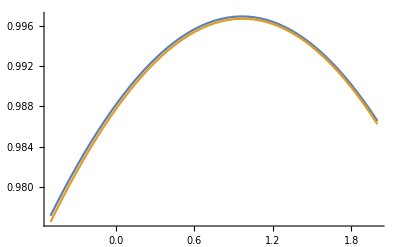

```mathematica
ListLinePlot[{realFidLand512,realFidLand}]
```

```mathematica
numSumTermsList={2,4,8};
TfStart=1.0;
TfEnd=7.0;
TfStep=0.25;
TfList0=Table[Tf,{Tf,TfStart,TfEnd,TfStep}];

TfStart=7.5;
TfEnd=16.0;
TfStep=0.5;
TfList1=Table[Tf,{Tf,TfStart,TfEnd,TfStep}];

TfList=Join[TfList0,TfList1];
```

```mathematica
TfList[[37]]
```

13.

```mathematica
GnList0=Import["./delta_lambdas/GnList_exp_comps=1_a=2417_U0(t).m.gz"];
```

```mathematica
GnList0={{0.,-1.1930902311003777-0.533314420977629 ⅈ,0.,-0.49208529979679283-0.5497837820077596 ⅈ,0.,0.003656542381750249+0.011390578331172383 ⅈ,0.,0.000022115710964850805-0.00019951698157510216 ⅈ},{0.,-0.9045091110631017-0.5244458293838163 ⅈ,0.,-0.2932782598446811-0.5123286495060542 ⅈ,0.,-0.00004229626751674201+0.009570530673947501 ⅈ,0.,0.00008128038766534966-0.00013850307710803385 ⅈ},{0.,-0.7038107010604986-0.5137257433057063 ⅈ,0.,-0.14997421815698053-0.46858814090115924 ⅈ,0.,-0.002504801244932695+0.0075721408335978155 ⅈ,0.,0.00010893361590328804-0.00007773662038028546 ⅈ},{0.,-0.5538012896187738-0.5012242873159805 ⅈ,0.,-0.04194252810120157-0.4196846506756892 ⅈ,0.,-0.0040524866333151105+0.005505843055948083 ⅈ,0.,0.00011243331038898409-0.000022733677846311508 ⅈ},{0.,-0.4359480035091818-0.4870230277084205 ⅈ,0.,0.04071372421614368-0.3668580662270784 ⅈ,0.,-0.00486429518511775+0.003481873660632425 ⅈ,0.,0.00009793377792934652+0.000021981205400379043 ⅈ},{0.,-0.3400070436843194-0.4712143379288424 ⅈ,0.,0.10342864457404709-0.311427739519934 ⅈ,0.,-0.005070161781461097+0.0016029670416843687 ⅈ,0.,0.0000715035989572729+0.00005335861112462459 ⅈ},{0.,-0.25987446413967147-0.4539006811432927 ⅈ,0.,0.14952444879974375-0.2547523703304932 ⅈ,0.,-0.004785735992432694-0.00004224103036752879 ⅈ,0.,0.00003915771693745655+0.00007010162751349433 ⅈ},{0.,-0.19169974022002823-0.43519381601289986 ⅈ,0.,0.18127761159043826-0.19818914298151422 ⅈ,0.,-0.0041247937186775305-0.0013846273493010018 ⅈ,0.,6.49639757151829*^-6+0.00007270763478859153 ⅈ},{0.,-0.13294221277784224-0.4152139323861117 ⅈ,0.,0.20044542310125077-0.14305347370855115 ⅈ,0.,-0.0032018186340082664-0.0023784360688590984 ⅈ,0.,-0.000021758121110480698+0.00006327815689172673 ⅈ},{0.,-0.08186275254482445-0.3940887242007114 ⅈ,0.,0.20853982331704637-0.09058069326783214 ⅈ,0.,-0.0021298828866356694-0.003003325289655763 ⅈ,0.,-0.000042169990318657736+0.000045132094858322255 ⅈ},{0.,-0.037233080730891974-0.37195240740497454 ⅈ,0.,0.20697185297842277-0.04189091053943528 ⅈ,0.,-0.0010163460382905086-0.0032645013041189886 ⅈ,0.,-0.00005285003278771399+0.000022283440580517175 ⅈ},{0.,0.0018387819441612724-0.34894469115502025 ⅈ,0.,0.19712477107421292+0.002041819169530925 ⅈ,0.,0.00004216844054283714-0.0031909869299394386 ⅈ,0.,-0.00005352012724144037-1.139071756548928*^-6 ⅈ},{0.,0.036017700208896095-0.3252097109199831 ⅈ,0.,0.18038542088572232+0.04041505796345958 ⅈ,0.,0.0009645640837562901-0.0028322142776393217 ⅈ,0.,-0.000045372762828690716-0.000021448081736438485 ⅈ},{0.,0.06581211647386323-0.3008949324248642 ⅈ,0.,0.15815009704969613+0.07261751114971551 ⅈ,0.,0.0016891711855458783-0.002253258002622525 ⅈ,0.,-0.0000307506346241282-0.00003585423497299937 ⅈ},{0.,0.0916211794920381-0.2761500355803287 ⅈ,0.,0.1318145403380106+0.09824196296648237 ⅈ,0.,0.0021763151590807957-0.0015291227018369702 ⅈ,0.,-0.00001269782960550023-0.00004276561281633227 ⅈ},{0.,0.11376695262739782-0.251125787687476 ⅈ,0.,0.10275421173248551+0.11709130551412927 ⅈ,0.,0.002409301503893917-0.0007385602272843781 ⅈ,0.,5.548766118407732*^-6-0.00004189736583322622 ⅈ},{0.,0.13251688802512324-0.2259729152626722 ⅈ,0.,0.07229907349945741+0.1291775878968755 ⅈ,0.,0.002393738329540206+0.000042085033178933065 ⅈ,0.,0.000021053338791604288-0.00003418774286585077 ⅈ},{0.,0.14809977798534205-0.20084098380267773 ⅈ,0.,0.04170597124067667+0.13471425588316463 ⅈ,0.,0.002155275552426012+0.0007445233657770593 ⅈ,0.,0.000031591324741433976-0.00002154479981999643 ⅈ},{0.,0.16071722815015244-0.1758772947037905 ⅈ,0.,0.01213098819869757+0.13410198645728544 ⅈ,0.,0.0017359779721443274+0.0013132367286377972 ⅈ,0.,0.00003592246307011906-6.471360220507637*^-6 ⅈ},{0.,0.17055198727546467-0.15122580836193372 ⅈ,0.,-0.015396364164709634+0.12790873808357783 ⅈ,0.,0.001189660473390981+0.001708932404390436 ⅈ,0.,0.00003389608147209093+8.368975567868747*^-6 ⅈ},{0.,0.1777740250052768-0.12702610221531574 ⅈ,0.,-0.03999565023880161+0.11684482869077499 ⅈ,0.,0.000576591268740951+0.0019105142591166655 ⅈ,0.,0.000026384289697335863+0.000020576753911238184 ⅈ},{0.,0.18254496558625144-0.10341237215013592 ⅈ,0.,-0.06095357699698843+0.10173401267018416 ⅈ,0.,-0.000041990925898572435+0.0019154810706220058 ⅈ,0.,0.000015064497096686583+0.00002836965634950568 ⅈ},{0.,0.1850213003463073-0.08051248527614385 ⅈ,0.,-0.07773679852624626+0.08348165017864508 ⅈ,0.,-0.000609099181851311+0.0017387932567513946 ⅈ,0.,2.0939825050564363*^-6+0.000030814999485952485 ⅈ},{0.,0.18535667856023735-0.05844709159654966 ⅈ,0.,-0.08999892349185468+0.06304114279510153 ⅈ,0.,-0.0010765505956824833+0.0014103734653380853 ⅈ,0.,-0.000010266909439674265+0.000027914120364025374 ⅈ},{0.,0.18370349290441157-0.03732880155048279 ⅈ,0.,-0.09758146777368885+0.041379846719982016 ⅈ,0.,-0.0014085093738310116+0.0009715127090597263 ⅈ,0.,-0.000020021774078849685+0.000020535102235741102 ⅈ},{0.,0.17504052306827855+0.001660647017086836 ⅈ,0.,-0.09897703712870835-0.0018645104049398859 ⅈ,0.,-0.001596710439090458-0.00004188982672838106 ⅈ,0.,-0.000026744513129394058-1.1382853652062541*^-6 ⅈ},{0.,0.16025588504897154+0.035742287926276116 ⅈ,0.,-0.08407917575151443-0.039448642200653965 ⅈ,0.,-0.0011865905518808743-0.000913836064071297 ⅈ,0.,-0.000015929461554079498-0.000019392401310874163 ⅈ},{0.,0.1405821435833261+0.06437067756686396 ⅈ,0.,-0.0571705468078061-0.06620574399752686 ⅈ,0.,-0.0003957182067382205-0.001353184486069774 ⅈ,0.,3.597896955693798*^-6-0.000023344585218616424 ⅈ},{0.,0.11725234431553645+0.08718013355316034 ⅈ,0.,-0.023841510614720413-0.07916184544543481 ⅈ,0.,0.00045106412346009554-0.0012530815189535432 ⅈ,0.,0.000018693159324584618-0.000012174890648107888 ⅈ},{0.,0.09148277040080531+0.10399031168117186 ⅈ,0.,0.00994225119718991-0.07774585778791474 ⅈ,0.,0.0010449080210067382-0.000707601066723737 ⅈ,0.,0.000020406203575293705+5.500611377491502*^-6 ⅈ},{0.,0.06445077601123433+0.11480565164274018 ⅈ,0.,0.03874892053571374-0.0636442743437397 ⅈ,0.,0.0011983877393276427+0.000041675115837172384 ⅈ,0.,9.037793829752382*^-6+0.000017929055797895364 ⅈ},{0.,0.037270426117374404+0.11980882817203974 ⅈ,0.,0.05843971379712325-0.04034344954108868 ⅈ,0.,0.0008990272815092048+0.0007046373270971077 ⅈ,0.,-6.980419365074642*^-6+0.00001780277882763327 ⅈ},{0.,0.010968035265131576+0.11934854934761073 ⅈ,0.,0.06667904689846044-0.012445331197421219 ⅈ,0.,0.00029721964508760116+0.0010493066485532491 ⅈ,0.,-0.000017105538572191188+6.370999669191577*^-6 ⅈ},{0.,-0.013540747327870304+0.11392223403381718 ⅈ,0.,0.06313797374155516+0.015129045183547084 ⅈ,0.,-0.00036167722957040243+0.0009787260879469272 ⅈ,0.,-0.000015454250078287876-8.12537245456558*^-6 ⅈ},{0.,-0.03547100469078954+0.10415426923274504 ⅈ,0.,0.04938117078044547+0.03792371282846414 ⅈ,0.,-0.0008328489063316321+0.000553823273496416 ⅈ,0.,-4.077514303786151*^-6-0.000016228448283154685 ⅈ},{0.,-0.05418476374012085+0.09077068959435738 ⅈ,0.,0.02847499741153899+0.052603669143829176 ⅈ,0.,-0.0009595128157770779-0.00004143543883537058 ⅈ,0.,8.99620853375901*^-6-0.000013308391545729968 ⅈ},{0.,-0.06920261233162499+0.07457123072168223 ⅈ,0.,0.004393618471746824+0.05739215199585558 ⅈ,0.,-0.0007222119939570957-0.0005758753643095921 ⅈ,0.,0.00001530396992414118-2.0909908902079946*^-6 ⅈ},{0.,-0.08021023562129528+0.056399781656463026 ⅈ,0.,-0.018673789667943072+0.052236824482685934 ⅈ,0.,-0.0002353249034139781-0.0008580334658432652 ⅈ,0.,0.000011330404183475553+9.636690266589158*^-6 ⅈ},{0.,-0.08705962793877502+0.037114297836788185 ⅈ,0.,-0.0370024888417676+0.03869636988708333 ⅈ,0.,0.0003041527103713098-0.0008024625814407708 ⅈ,0.,3.645618635084318*^-7+0.000014338581553697196 ⅈ},{0.,-0.08976496731341639+0.017557233091848565 ⅈ,0.,-0.047894272081203726+0.01958212575080341 ⅈ,0.,0.0006939261899609579-0.0004531869973928252 ⅈ,0.,-0.000010079652397834663+9.496792525681114*^-6 ⅈ},{0.,-0.08849335627416297-0.0014724914750661058 ⅈ,0.,-0.05004191557843285-0.001574875180046447 ⅈ,0.,0.0008003364566539775+0.000041194594473390685 ⅈ,0.,-0.000013338998465513204-1.1358673973799953*^-6 ⅈ},{0.,-0.08355083034449719-0.019245040529568398 ⅈ,0.,-0.043650610434150104-0.021137896846318664 ⅈ,0.,0.0006025371800374581+0.0004886265939087444 ⅈ,0.,-7.791590555558444*^-6-0.000010350694963253619 ⅈ},{0.,-0.07536421008623576-0.035121907567025684 ⅈ,0.,-0.030311219324748687-0.035958345486170266 ⅈ,0.,0.00019286813963515355+0.0007265709385331445 ⅈ,0.,2.435815097708149*^-6-0.000012312115638413015 ⅈ}};
```

```mathematica
Table[GnList[i]=GnList0[[i]],{i,1,Length[TfList]}];
```

```mathematica
For[l=1,l≤Length[numSumTermsList],l++,
For[i=1,i≤Length[TfList],i++,
FidApproxList[l][i]=1-Sum[Abs[GnList[i][[k]]]^2,{k,1,numSumTermsList[[l]]}];

fidList[l]=Table[FidApproxList[l][i],{i,1,Length[TfList]}];
fidListPlot[l]=Table[{TfList[[i]],fidList[l][[i]]},{i,1,Length[TfList]}];
]
]
```

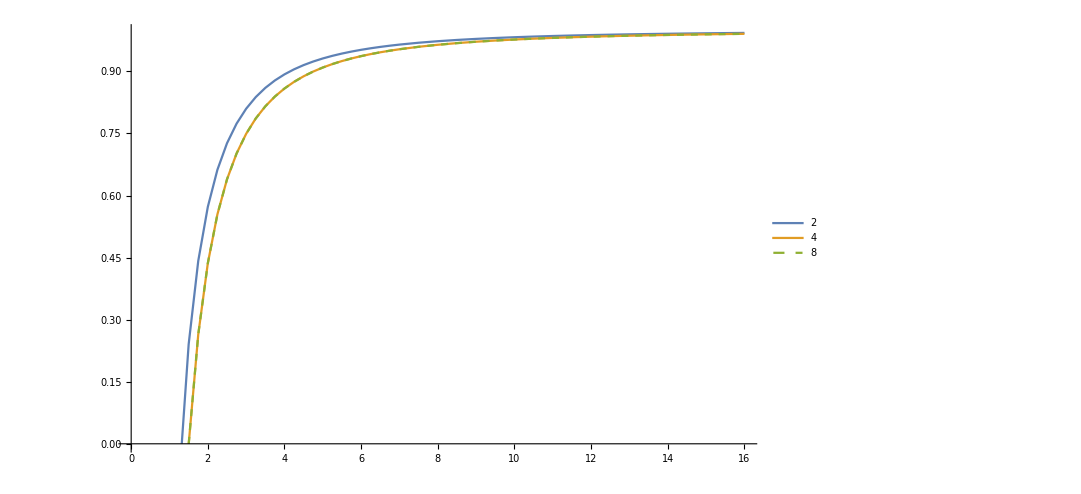

```mathematica
ListLinePlot[Table[fidListPlot[l],{l,1,Length[numSumTermsList]}],PlotLegends->numSumTermsList,PlotStyle->{,,Dashed,Dotted},ImageSize->800]
```

```mathematica
numComps=1;
KnList0=Import["./delta_lambdas/KnHmuList_exp_comps=1_a=2417_U0(t)_Tfover2.m.gz"]
```

```mathematica
KnList0={{0.,8.180804625626797+3.5970077668964255 ⅈ,0.,-0.06980033306167041-0.07721415437085408 ⅈ,0.,0.0004601758437207973+0.0014182241044132745 ⅈ,0.,2.5209711927081617*^-6-0.00002332402597185061 ⅈ},{0.,9.705814684231589+5.529007376993323 ⅈ,0.,-0.06533040404326498-0.11251392161519354 ⅈ,0.,-9.411685055111236*^-7+0.0018637220188986274 ⅈ,0.,0.000014755461533792289-0.000025341154774601772 ⅈ},{0.,10.897858794316374+7.802789800200102 ⅈ,0.,-0.04868327458563241-0.14833730507744325 ⅈ,0.,-0.0006923754025305601+0.0021265245319846194 ⅈ,0.,0.000028558531941797017-0.000020556703273771932 ⅈ},{0.,11.703899254190665+10.368055097957384 ⅈ,0.,-0.019663034028955726-0.1810709854794808 ⅈ,0.,-0.0015350513587793356+0.0021096753580271493 ⅈ,0.,0.000040196981309898106-8.32766105437006*^-6 ⅈ},{0.,12.077949883193734+13.16734146961413 ⅈ,0.,0.020941418244727394-0.2070900270686562 ⅈ,0.,-0.002413620061788866+0.001750614525731177 ⅈ,0.,0.000045829259338021514+0.000010024053740373436 ⅈ},{0.,11.981972787300782+16.13696647904896 ⅈ,0.,0.07137014590950125-0.22301146331804877 ⅈ,0.,-0.0031909770689107094+0.001033597403539229 ⅈ,0.,0.000042488380342994496+0.00003130228439063011 ⅈ},{0.,11.386653828833872+19.208075217342472 ⅈ,0.,0.12896855297000384-0.2259395238519011 ⅈ,0.,-0.003726698801272953-3.7765466658204975*^-6 ⅈ,0.,0.000028942099126167403+0.00005099349818822402 ⅈ},{0.,10.272044491154736+22.30778018152168 ⅈ,0.,0.19032304684218296-0.21368755784614143 ⅈ,0.,-0.0038970999836858565-0.0012710534695151026 ⅈ,0.,6.221126165084791*^-6+0.00006419276353298256 ⅈ},{0.,8.628059699098326+25.36037627134169 ⅈ,0.,0.2514492011334612-0.18496281576952966 ⅈ,0.,-0.0036143291848597155-0.0026326979699657052 ⅈ,0.,-0.000022330847556340667+0.00006671333307085258 ⅈ},{0.,6.454823176499743+28.28861315381475 ⅈ,0.,0.3080224982767834-0.13950214258363083 ⅈ,0.,-0.0028419473635922315-0.003922493777185932 ⅈ,0.,-0.0000515337020748514+0.00005614238379621653 ⅈ},{0.,3.7628540665957204+31.01500633488512 ⅈ,0.,0.3556391058733561-0.07814921706505297 ⅈ,0.,-0.001604779708224292-0.004963050676786045 ⅈ,0.,-0.00007530927160880997+0.00003260253398034017 ⅈ},{0.,0.5730907807748868+33.46316762225913 ⅈ,0.,0.39009216977949207-0.0028671119251619916 ⅈ,0.,8.540030868004741*^-6-0.0055881899620465565 ⅈ,0.,-0.0000879118095596229-9.725267164069055*^-7 ⅈ},{0.,-3.08324965379021+35.55913527258256 ⅈ,0.,0.407647906358744+0.08331651483685634 ⅈ,0.,0.0018510693671621628-0.005665523829082884 ⅈ,0.,-0.0000852064476322103-0.00003914764465237612 ⅈ},{0.,-7.164976137511911+37.23268399608933 ⅈ,0.,0.4053054210627957+0.1764305407892501 ⅈ,0.,0.0037308736323601924-0.005116398595001895 ⅈ,0.,-0.00006572489838321597-0.00007486190089826391 ⅈ},{0.,-11.621388979913856+38.41859514515809 ⅈ,0.,0.38102470191094145+0.2717429976986777 ⅈ,0.,0.005430959552628815-0.003930564010172347 ⅈ,0.,-0.00003125647153531307-0.00010073008338171057 ⅈ},{0.,-16.392901052127836+39.05786783892904 ⅈ,0.,0.33390861991936843+0.36399680551146263 ⅈ,0.,0.0067337611927467695-0.002173448856785982 ⅈ,0.,0.00001318651794892905-0.00011053078234981552 ⅈ},{0.,-21.411807088465427+39.09885246969492 ⅈ,0.,0.26432695388474214+0.44768705536410963 ⅈ,0.,0.007447461999478459+0.000015284414363652214 ⅈ,0.,0.00006007080472704086-0.00010058695065155669 ⅈ},{0.,-26.603191450672956+38.49828899007185 ⅈ,0.,0.17397334095741399+0.5173656521480019 ⅈ,0.,0.007431082402037363+0.0024322504270341432 ⅈ,0.,0.00010061891068069472-0.00007074705968869445 ⅈ},{0.,-31.88596262370195+37.22223358142276 ⅈ,0.,0.06584949580894903+0.5679572144615541 ⅈ,0.,0.006615257299321017+0.00482919723913761 ⅈ,0.,0.00012644421778424997-0.000024737011439701522 ⅈ},{0.,-37.17400081481345+35.24685873877291 ⅈ,0.,-0.05582513273103644+0.5950690422822131 ⅈ,0.,0.005015984627931601+0.00693846457693181 ⅈ,0.,0.00013124111594680382+0.00003023476869297352 ⅈ},{0.,-42.37740330480661+32.55911345752598 ⅈ,0.,-0.18577608334379123+0.5952777737488602 ⅈ,0.,0.0027393164840792653+0.008502437009165567 ⅈ,0.,0.00011219608510897727+0.00008459415589667375 ⅈ},{0.,-47.403810675163875+29.15723205174654 ⅈ,0.,-0.31790280177571645+0.5663760897412409 ⅈ,0.,-0.00002407986038381859+0.00930378852490736 ⅈ,0.,0.00007081978259254914+0.00012806944205132395 ⅈ},{0.,-52.15979572949592+25.05108214906391 ⅈ,0.,-0.4455638117182881+0.5075644684148022 ⅈ,0.,-0.0030144426597341007+0.009193063545679843 ⅈ,0.,0.00001299603738692901+0.0001516199959865588 ⅈ},{0.,-56.55229586062669+20.262344567460293 ⅈ,0.,-0.5619048569434001+0.41957547404354056 ⅈ,0.,-0.00592730598115637+0.008110274813628138 ⅈ,0.,-0.00005181472785512945+0.00014926529184748752 ⅈ},{0.,-60.490068801725855+14.824520056387362 ⅈ,0.,-0.6602140174792839+0.304721273357872 ⅈ,0.,-0.00844447231662662+0.0060977198725233215 ⅈ,0.,-0.00011211829729064951+0.00011945164985399855 ⅈ},{0.,-66.65429880938467+2.193522594821361 ⅈ,0.,-0.7787756033300519+0.011271613522836059 ⅈ,0.,-0.011156451362092172-0.00003501374068985435 ⅈ,0.,-0.00017542219734412455-3.893782830083781*^-6 ⅈ},{0.,-70.01375924953238-12.348309790729022 ⅈ,0.,-0.763836543407396-0.3260794331321492 ⅈ,0.,-0.009600817970409221-0.007024856107130274 ⅈ,0.,-0.00012186033361083384-0.00014196164873099548 ⅈ},{0.,-70.04849061765643-28.14708864533407 ⅈ,0.,-0.6008977073435272-0.6458388225106055 ⅈ,0.,-0.003861425161101617-0.012031063884617606 ⅈ,0.,0.000025739186968549508-0.00019702863667550848 ⅈ},{0.,-66.39582008120607-44.418118116180096 ⅈ,0.,-0.3038097031165363-0.8829121981044239 ⅈ,0.,0.0041813388605062025-0.012703461736040934 ⅈ,0.,0.00017337306365893755-0.00011902850530096773 ⅈ},{0.,-58.88147639665251-60.28430839917234 ⅈ,0.,0.08517039489775889-0.9815522654292886 ⅈ,0.,0.011449937867410876-0.008248139218789731 ⅈ,0.,0.0002156466129900108+0.00005222870296192124 ⅈ},{0.,-47.54129238764484-74.8216640476584 ⅈ,0.,0.5011323944931108-0.9075375062132338 ⅈ,0.,0.01484796604852181+0.00006372534920440905 ⅈ,0.,0.00011067126876537391+0.0002055457949028011 ⅈ},{0.,-32.6319495925864-87.10955093843185 ⅈ,0.,0.867346768595392-0.6570379798526994 ⅈ,0.,0.012565949299106033+0.009216999051472939 ⅈ,0.,-0.00008293719720837331+0.00023052894628967948 ⅈ},{0.,-14.629774907476468-96.283121092051 ⅈ,0.,1.109370460219344-0.26012825416935587 ⅈ,0.,0.004968548281852964+0.015543839197127101 ⅈ,0.,-0.0002376325796030592+0.00009661961798315859 ⅈ},{0.,5.782780355861622-101.58508269413662 ⅈ,0.,1.169839408173894+0.2221492180283985 ⅈ,0.,-0.005350888704434881+0.016191115427196867 ⅈ,0.,-0.00024098932474335172-0.00011733251941282306 ⅈ},{0.,27.742693953544567-102.4139560903856 ⅈ,0.,1.0210581392402016+0.7070499983654902 ⅈ,0.,-0.014443415185381402+0.010377786001376399 ⅈ,0.,-0.00007682555953909018-0.0002687615903951397 ⅈ},{0.,50.24301863745608-98.36606044820587 ⅈ,0.,0.6727494540346277+1.1043399837277375 ⅈ,0.,-0.018516482709556324-0.00010241042196476187 ⅈ,0.,0.00015478414214606796-0.00024641669502796813 ⅈ},{0.,72.17905910242568-89.26872774557852 ⅈ,0.,0.17311520325216934+1.3330104576623767 ⅈ,0.,-0.015505606753600493-0.011403236931564751 ⅈ,0.,0.00029805298484045884-0.00005136510229354463 ⅈ},{0.,92.4019639190057-75.202630641971 ⅈ,0.,-0.39744558304263633+1.3374119332774188 ⅈ,0.,-0.006057983011275719-0.019035914072449967 ⅈ,0.,0.0002462884435478316+0.00019457365979935127 ⅈ},{0.,109.7771586705735-56.51162127194108 ⅈ,0.,-0.93922588960469+1.0996495802658492 ⅈ,0.,0.006522477901074182-0.019650538688237268 ⅈ,0.,0.00002043904920386123+0.0003246357739707706 ⅈ},{0.,123.24471132722698-33.79908522789295 ⅈ,0.,-1.3506499458607681+0.6456192206529529 ⅈ,0.,0.017421237749924986-0.012482576398104748 ⅈ,0.,-0.00023590698011644794+0.0002401821349906404 ⅈ},{0.,131.87852818255956-7.910489778089499 ⅈ,0.,-1.5472099134698558+0.043134632664899475 ⅈ,0.,0.022156676357232282+0.0001522541559969588 ⅈ,0.,-0.00034766472405468017-0.000015628437863132952 ⅈ},{0.,134.9412414732281+20.097485481143895 ⅈ,0.,-1.4783868626033558-0.6079764908635495 ⅈ,0.,0.01841479975927526+0.01358145206292272 ⅈ,0.,-0.00022778559715883805-0.00027792801282142533 ⅈ},{0.,131.9317734631806+49.0001393552062 ⅈ,0.,-1.1392312814546515-1.192406169483398 ⅈ,0.,0.007126918476273654+0.022502693731849006 ⅈ,0.,0.000056393493092126064-0.0003663370037574625 ⅈ}};
```

```mathematica
Table[KnHmuList[i]=KnList0[[i]],{i,1,Length[TfList]}];
```

```mathematica
For[l=1,l≤3,l++,
For[i=1,i≤Length[TfList],i++,
Tf=TfList[[i]];
epsilon0Approx[l][i]=-(Sum[Abs[GnList[i][[k]]]^2,{k,1,numSumTermsList[[l]]}])*(Re[Sum[GnList[i][[k]]*Conjugate[KnHmuList[i][[k]]],{k,1,numSumTermsList[[l]]}]])*(1.0/Sum[Re[GnList[i][[k]]*Conjugate[KnHmuList[i][[k]]]],{k,1,numSumTermsList[[l]]}]^2);


gradApproxHmu[l][i]=-2*Re[Sum[GnList[i][[k]]*Conjugate[KnHmuList[i][[k]]],{k,1,numSumTermsList[[l]]}]];

epsilon0Approx2[l][i]=(2(1-FidApproxList[l][i]))/Norm[gradApproxHmu[l][i]]^2 gradApproxHmu[l][i];

epsNorm[l][i]=Norm[gradApproxHmu[l][i]];
normalisedGrad[l][i]=gradApproxHmu[l][i]/Norm[gradApproxHmu[l][i]];

zMatrix0[l][i]=-2Re[
Sum[KnHmuList[i][[j]]*Conjugate[KnHmuList[i][[j]]]
,{j,1,numSumTermsList[[l]]}]
];

zMatrix[l][i]=-2Re[
Sum[
KnHmuList[i][[j]]*Conjugate[KnHmuList[i][[j]]]
,{j,1,numSumTermsList[[l]]}]
];

epsilonZ[l][i]=-(zMatrix[l][i])^(-1)*gradApproxHmu[l][i];

epsilonCorr02[l][i]=(Norm[gradApproxHmu[l][i]]/Abs[(normalisedGrad[l][i]*zMatrix0[l][i]*normalisedGrad[l][i])])*normalisedGrad[l][i];
epsilonCorr2[l][i]=(Norm[gradApproxHmu[l][i]]/Abs[(normalisedGrad[l][i]*zMatrix[l][i]*normalisedGrad[l][i])])*normalisedGrad[l][i];

If[i==1,
Print["l = ",l," i = ",i," Tf = ",TfList[[i]]
,"\n FidApprox = ",fidList[l][[i]]
,"\n zMatrix[l][i] = ",zMatrix[l][i]
,"\n epsilonZ[l][i] = ",epsilonZ[l][i]
,"\n epsilon0Approx = ",epsilon0Approx[l][i]
,"\n epsilonCorr02 = ",epsilonCorr02[l][i]
,"\n epsilonCorr2 = ",epsilonCorr2[l][i]
];
];
];
];
```

l = 1 i = 1 Tf = 1.
 FidApprox = -0.707889
 zMatrix[l][i] = -159.728
 epsilonZ[l][i] = 0.146233
 epsilon0Approx = 0.146239
 epsilonCorr02 = 0.146233
 epsilonCorr2 = 0.146233

l = 2 i = 1 Tf = 1.
 FidApprox = -1.2523
 zMatrix[l][i] = -159.75
 epsilonZ[l][i] = 0.145252
 epsilon0Approx = 0.194131
 epsilonCorr02 = 0.145252
 epsilonCorr2 = 0.145252

l = 3 i = 1 Tf = 1.
 FidApprox = -1.25244
 zMatrix[l][i] = -159.75
 epsilonZ[l][i] = 0.145252
 epsilon0Approx = 0.194143
 epsilonCorr02 = 0.145252
 epsilonCorr2 = 0.145252

```mathematica
tfNum0=37;
TfList[[tfNum0]]
```

13.

```mathematica
tfNum=26;
```

```mathematica
STAlist[[tfNum0]]
```

{13.,0.987738}

```mathematica
eSTA1storder1comp[[tfNum0]]
```

{13.,0.995305}

```mathematica
eSTA2ndorder1comp[[tfNum0]]
```

{13.,0.996685}

```mathematica
realFidSTA=STAlist[[tfNum0,2]]
realFideSTA=eSTA2ndorder1comp[[tfNum0,2]]
```

0.987738

0.996685

```mathematica
l=2;i=tfNum0;
Print["l = ",l," i = ",i," Tf = ",TfList[[i]]
,"\n FidApprox = ",fidList[l][[i]]
,"\n zMatrix[l][i] = ",zMatrix[l][i]
,"\n epsilonZ[l][i] = ",epsilonZ[l][i]
,"\n epsilon0Approx = ",epsilon0Approx[l][i]
,"\n epsilonCorr02 = ",epsilonCorr02[l][i]
,"\n epsilonCorr2 = ",epsilonCorr2[l][i]
];
```

l = 2 i = 37 Tf = 13.
 FidApprox = 0.986337
 zMatrix[l][i] = -26361.1
 epsilonZ[l][i] = 0.000878158
 epsilon0Approx = 0.00118043
 epsilonCorr02 = 0.000878158
 epsilonCorr2 = 0.000878158

l = 2 i = 37 Tf = 13.
 FidApprox = 0.986337\n zMatrix[l][i] = -26361.1
 epsilonZ[l][i] = 0.000878158
 epsilon0Approx = 0.00118043
 epsilonCorr02 = 0.000878158
 epsilonCorr2 = 0.000878158

```mathematica
eps=epsilonCorr2[2][tfNum0]
eps0=epsilon0Approx2[2][tfNum0]
```

0.000878158

0.00118043

```mathematica
aa=zMatrix[2][tfNum0]
bb=gradApproxHmu[2][tfNum0]
c=FidApproxList[2][tfNum0]
```

-26361.1

23.1492

0.986337

```mathematica
g[x_]=a1 x^2+b1 x+ c1;
```

```mathematica
Solve[{g'[x]==0},x]
```

{{x→-b1/(2 a1)}}

```mathematica
Solve[(2(1-c1))/b1==-b1/(2 a1),a1]
```

{{a1→b1^2/(4 (-1+c1))}}

```mathematica
b1=bb;c1=c;
```

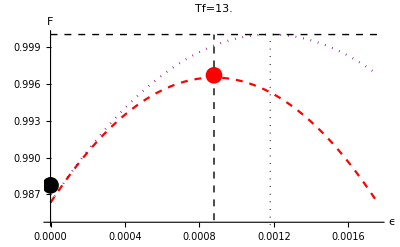

```mathematica
pl=Plot[{
aa/2*x^2+bb*x+c
,
b1^2/(4 (-1+c1))*x^2+b1*x+c1
},{x,0,2eps}
,PlotRange->{c-0.0016,1}
,AxesLabel->{"ϵ","F"}
,PlotLabel->StringForm["Tf=``",TfList[[tfNum0]]]
,PlotStyle->{{Red,Dashed},{Purple,Dotted}}
,Epilog->{
{Dashed,Line[{{eps,0},{eps,1}}]}
,
{Dotted,Line[{{eps0,0},{eps0,1}}]}
,
{Dashed,Line[{{0,1},{2eps,1}}]}
,
{PointSize[0.03],{Red,Point[{eps,realFideSTA}]},Point[{0,realFidSTA}]}
}
]
```

```mathematica
realFidLand0=Drop[realFidLand,10];
```

```mathematica
realFidLand00=Table[{eps*realFidLand0[[i,1]],realFidLand0[[i,2]]},{i,1,Length[realFidLand0]}];
```

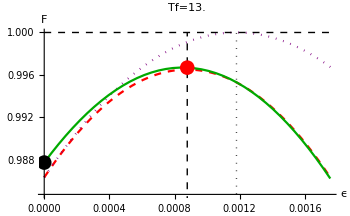

```mathematica
plot1=Show[{pl,ListLinePlot[realFidLand00,PlotStyle->Darker@Green]},ImageSize->350]
```

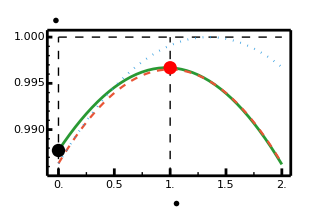

```mathematica
classColour=RGBColor[0.915, 0.3325, 0.2125];
minAnharmColour=RGBColor[0.16, 0.6, 0.2];
polyColour=RGBColor[0.16, 0.6, 0.88];
colNum1=1;
colNum2=2;
(*** Plot window ***)
xMin=0;xMax=2.03*eps;
yMin=0.985;yMax=1.0;
(*** Frame window offsets ***)
xoffset=0.1*eps;
yoffset=0.00075;
xoffsetRight=0.0;

aspectRatio=0.7;
imageSize=320;
ratio=500/imageSize;

fontSize=14;
matexMag=2;
gridThickness=0.0001;

axesThickness=ratio*0.004;
plotThickness=ratio*0.004;

tickMajorThickness=ratio*0.004;
tickMinorThickness=tickMajorThickness/2;

yLabelOffset=0.0;
yTickMajorList=Table[i,{i,0.99,1.0,0.005}];
ytickMajorLength=0.4*10^(-4);
yTickMinorList=Table[i,{i,0.986,0.999,0.001}];
ytickMinorLength=ytickMajorLength/2;

xTickMajorList=Table[i,{i,0,2eps,0.5eps}];
xtickMajorHeight=0.0008;
xTickMinorList=Table[i,{i,0.25eps,1.75eps,0.5 eps}];
xtickMinorHeight=xtickMajorHeight/2;
xLabelSteps=Length[xTickMajorList];

plotOutputsinSq=
ListLinePlot[{
realFidLand00
}
,PlotRange->{{0,xMax},{yMin,yMax}}
,PlotStyle->{
{minAnharmColour, Thickness[plotThickness]}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,Frame->False
,Axes->False
];

plot11=Plot[{aa/2*x^2+bb*x+c
,
b1^2/(4 (-1+c1))*x^2+b1*x+c1},{x,0,2eps}
,PlotRange->{{0,xMax},{yMin,yMax}}
,PlotStyle->{{classColour,Dashed},{polyColour,Dotted}}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,Frame->False
,Axes->False];
frame=Graphics[{
(*** Dashed F=1 Line ***)
{
{AbsoluteDashing[6],Line[{{0,yMin},{0,1.0}}]}
,
{AbsoluteDashing[6],Line[{{0,1.0},{2 eps,1}}]}
,
{AbsoluteDashing[6],Line[{{eps,yMin},{eps,1}}]}
}
,
(*** Frame ***)
{
Thickness[axesThickness]
,Line[{{xMin-xoffset,yMin},{xMax+xoffset/2,yMin}}]
,Line[{{xMax+xoffset/2,yMin},{xMax+xoffset/2,yMax+yoffset}}]
,Line[{{xMax+xoffset/2,yMax+yoffset},{xMin-xoffset,yMax+yoffset}}]
,Line[{{xMin-xoffset,yMax+yoffset},{xMin-xoffset,yMin}}]
}
,
{
(*** Ticks Major ***)
Thickness[tickMajorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMajorHeight}}],{i,xTickMajorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMajorLength,i}}],{i,yTickMajorList}]
}
,
{
(*** Ticks Minor ***)
Thickness[tickMinorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMinorHeight}}],{i,xTickMinorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMinorLength,i}}],{i,yTickMinorList}]
}
,
{
(*** Tick Major values ***)
(* x-axis *)Table[Inset[i/eps,{i,yMin-0.001}],{i,xTickMajorList}]
,
(* y-axis *)Table[Inset[NumberForm[i,{4,3}],{xMin-0.00023,i}],{i,yTickMajorList}]
}
,
{
(*** Axes labels ***)
(* x-axis *)Inset[MaTeX["\\epsilon / \\epsilon_s^{(2)}",Magnification->matexMag],{eps+0.00005,yMin-0.003}]
,
(* y-axis *)Inset[MaTeX["F",Magnification->matexMag],{xMin-0.00002,yMax+0.0018}]
}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,LabelStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman",Black}
,AspectRatio->aspectRatio
,ImageSize->imageSize
];

mainPlotsinSqInset0=Show[frame,plotOutputsinSq,plot11,Epilog->{
{PointSize[0.03],{Red,Point[{eps,realFideSTA}]},Point[{0,realFidSTA}]}}]
```

```mathematica
exportPlot=Show[
mainPlotsinSq0,
(*** Inset Plot ***)
Epilog->
{
Inset[mainPlotsinSqInset0,{10.5,0.882}]
}]
```

-Graphics-

```mathematica
Export["fig_fid_gaussian_v2.pdf",exportPlot]
```

fig_fid_gaussian_v2.pdf

Opt Control plot

```mathematica
optSTAraw=Import["./Global_Output/OPT2_open_exp_a=2417.82_L=200_gamma=10_sumTerms=4_numComps=8_eSTA_hess_1e4steps/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_STA.dat"]
```

```mathematica
optSTAraw={{"#tfinal","#cabs2_fidelity_sta"},{1.,0.7851176},{1.25,0.8328381},{1.5,0.8616479},{1.75,0.8753977},{2.,0.8918451},{2.25,0.9021811},{2.5,0.9140282},{2.75,0.9208026},{3.,0.9299406},{3.25,0.9359721},{3.5,0.9444457},{3.75,0.9487606},{4.,0.9557248},{4.25,0.956507},{4.5,0.959817},{4.75,0.9649167},{5.,0.966058},{5.25,0.968102},{5.5,0.9718758},{5.75,0.9747304},{6.,0.975307},{6.25,0.9781439},{6.5,0.979702},{6.75,0.9801319},{7.,0.9828758},{7.25,0.9840542},{7.5,0.9854196},{7.75,0.9849108},{8.,0.9853851},{8.25,0.9873512},{8.5,0.9868057},{8.75,0.9885575},{9.,0.9881093},{9.25,0.9907018},{9.5,0.9892175},{9.75,0.9911401},{10.,0.9915517},{10.25,0.9907509},{10.5,0.991717},{10.75,0.9911377},{11.,0.9926927},{11.25,0.9932872},{11.5,0.9929912},{11.75,0.9948835},{12.,0.9934009},{12.25,0.9938901},{12.5,0.9937386},{12.75,0.993372},{13.,0.9950092},{13.25,0.9935991},{13.5,0.9946911},{13.75,0.9951356},{14.,0.9953897},{14.25,0.995449},{14.5,0.9949238},{14.75,0.9970785},{15.,0.9962055},{15.25,0.9950925},{15.5,0.9965521},{15.75,0.997598},{16.,0.9960281}};
```

```mathematica
opt3STAraw=Import["./Global_Output/OPT3_open_exp_a=2417.82_L=200_gamma=10_sumTerms=4_numComps=8_eSTA_hess_1e4steps/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_STA.dat"]
```

```mathematica
opt3STAraw={{"#tfinal","#cabs2_fidelity_sta"},{1.,0.7978396},{1.25,0.8242887},{1.5,0.8529011},{1.75,0.8753976},{2.,0.8930563},{2.25,0.9021811},{2.5,0.9140281},{2.75,0.9243443},{3.,0.9306952},{3.25,0.9387454},{3.5,0.943844},{3.75,0.9487605},{4.,0.9537957},{4.25,0.956507},{4.5,0.961409},{4.75,0.9634909},{5.,0.966058},{5.25,0.9689079},{5.5,0.9718758},{5.75,0.974458},{6.,0.9767362},{6.25,0.9781439},{6.5,0.979702},{6.75,0.981117},{7.,0.9826549},{7.25,0.9830438},{7.5,0.9841939},{7.75,0.9861576},{8.,0.9866626},{8.25,0.9875366},{8.5,0.9881076},{8.75,0.9885575},{9.,0.9894263},{9.25,0.9894368},{9.5,0.9903902},{9.75,0.9911401},{10.,0.9915517},{10.25,0.9922224},{10.5,0.9915721},{10.75,0.9926516},{11.,0.9926927},{11.25,0.9932871},{11.5,0.9931192},{11.75,0.9935236},{12.,0.9932777},{12.25,0.9938901},{12.5,0.9938554},{12.75,0.9946866},{13.,0.9951091},{13.25,0.9950534},{13.5,0.9945881},{13.75,0.9952314},{14.,0.9954814},{14.25,0.9953584},{14.5,0.9963916},{14.75,0.995762},{15.,0.9962828},{15.25,0.996538},{15.5,0.9965521},{15.75,0.9963909},{16.,0.9960281}};
```

```mathematica
opt4STAraw=Import["./Global_Output/OPT4_more_x_steps_open_exp_a=2417.82_L=200_gamma=10_sumTerms=4_numComps=8_eSTA_hess_1e4steps/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_STA.dat"]
```

```mathematica
opt4STAraw={{"#tfinal","#cabs2_fidelity_sta"},{1.,0.7952371},{1.25,0.8217977},{1.5,0.8505622},{1.75,0.8732108},{2.,0.8910143},{2.25,0.9002313},{2.5,0.9122029},{2.75,0.9226395},{3.,0.9290747},{3.25,0.9372355},{3.5,0.9424128},{3.75,0.9474089},{4.,0.952528},{4.25,0.9552932},{4.5,0.9602836},{4.75,0.9624108},{5.,0.9650317},{5.25,0.9679396},{5.5,0.9709737},{5.75,0.9736178},{6.,0.9759516},{6.25,0.9773978},{6.5,0.978999},{6.75,0.980454},{7.,0.982034},{7.25,0.9824391},{7.5,0.9836249},{7.75,0.9856388},{8.,0.9861625},{8.25,0.9870646},{8.5,0.987655},{8.75,0.9881233},{9.,0.9890182},{9.25,0.989037},{9.5,0.9900191},{9.75,0.99079},{10.,0.9912208},{10.25,0.9919101},{10.5,0.9912499},{10.75,0.9923603},{11.,0.9924088},{11.25,0.9930221},{11.5,0.9928518},{11.75,0.993272},{12.,0.9930236},{12.25,0.9936524},{12.5,0.993621},{12.75,0.99448},{13.,0.9949148},{13.25,0.9948624},{13.5,0.9943885},{13.75,0.9950485},{14.,0.9953071},{14.25,0.995187},{14.5,0.9962477},{14.75,0.9956044},{15.,0.9961389},{15.25,0.9964027},{15.5,0.9964221},{15.75,0.9962578},{16.,0.9958839}};
```

```mathematica
TfList=Table[i,{i,1,16,0.25}];
num=Length[TfList];
optSTA=Table[{optSTAraw[[i,1]],optSTAraw[[i,2]]},{i,2,Length[optSTAraw]}];
opt3STA=Table[{opt3STAraw[[i,1]],opt3STAraw[[i,2]]},{i,2,Length[opt3STAraw]}];
opt4STA=Table[{opt4STAraw[[i,1]],opt4STAraw[[i,2]]},{i,2,Length[opt4STAraw]}];
```

```mathematica
STAOpt=Import["./Global_Output/OPT_t_steps=1e5_x_steps=1024_open_exp_a=2417.82_L=200_gamma=10_sumTerms=4_numComps=8/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_STA_opt.dat"]
```

```mathematica
STAOpt={{"#tfinal","#cabs2_fidelity_sta"},{1.,0.7885425},{1.25,0.8243047},{1.5,0.8529951},{1.75,0.8732108},{2.,0.8886575},{2.25,0.9020826},{2.5,0.9125846},{2.75,0.9222685},{3.,0.9301819},{3.25,0.9366794},{3.5,0.9425347},{3.75,0.9482951},{4.,0.9527257},{4.25,0.9561945},{4.5,0.9594831},{4.75,0.9628537},{5.,0.9656998},{5.25,0.9677763},{5.5,0.9703973},{5.75,0.9732093},{6.,0.9751922},{6.25,0.9772959},{6.5,0.978999},{6.75,0.9802548},{7.,0.9815833},{7.25,0.9831519},{7.5,0.9839651},{7.75,0.9853095},{8.,0.9858288},{8.25,0.9870275},{8.5,0.9873221},{8.75,0.9881233},{9.,0.988688},{9.25,0.9893709},{9.5,0.9897848},{9.75,0.99073},{10.,0.9907475},{10.25,0.9916225},{10.5,0.9918258},{10.75,0.9920653},{11.,0.9924609},{11.25,0.9930221},{11.5,0.9928268},{11.75,0.9935681},{12.,0.9936143},{12.25,0.9936072},{12.5,0.9941658},{12.75,0.9942236},{13.,0.9943446},{13.25,0.9945827},{13.5,0.9950207},{13.75,0.9950304},{14.,0.9952899},{14.25,0.9952042},{14.5,0.9954189},{14.75,0.9959016},{15.,0.9961248},{15.25,0.9961037},{15.5,0.9964221},{15.75,0.9965352},{16.,0.9964478}};
```

```mathematica
STAOpt1=Drop[STAOpt,1];
```

```mathematica
omega0=2500*2*Pi;
const=10^(-3)*omega0;
0.1*const
1.0*const
```

1.5708

15.708

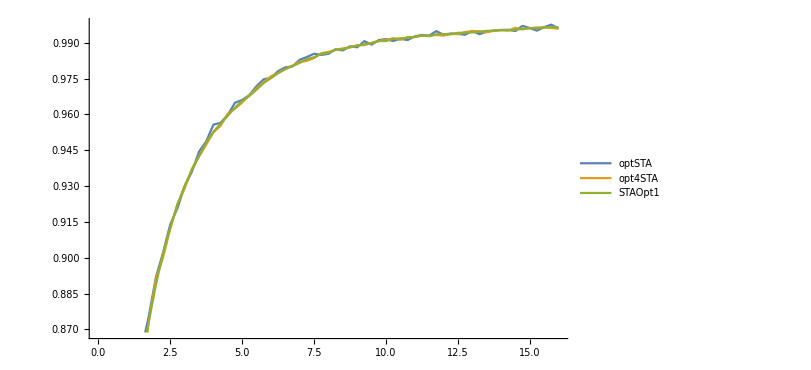

```mathematica
ListLinePlot[{optSTA,opt4STA,STAOpt1},PlotLegends->{"optSTA","opt4STA","STAOpt1"},ImageSize->600]
```

```mathematica
Table[{opt4STA[[i,1]]/const,opt4STA[[i,2]]},{i,2,Length[opt4STA]}];
```

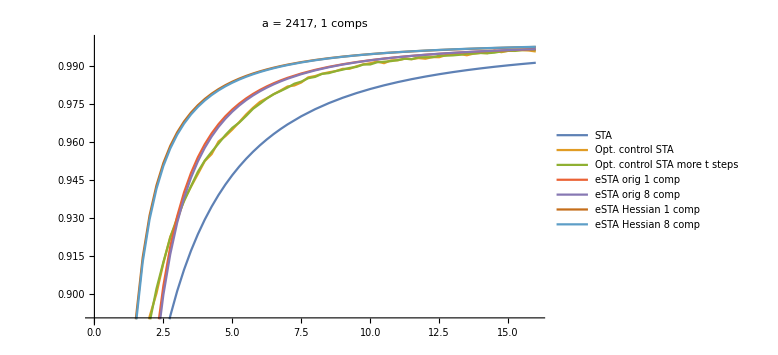

```mathematica
ListLinePlot[{
STAlist
,opt4STA
,STAOpt1
,eSTA1storder1comp,eSTA1storder8comp,eSTA2ndorder1comp,eSTA2ndorder8comp
}
,PlotLegends->{"STA","Opt. control STA","Opt. control STA more t steps","eSTA orig 1 comp","eSTA orig 8 comp","eSTA Hessian 1 comp","eSTA Hessian 8 comp"}
,PlotLabel->"a = 2417, 1 comps"
,PlotRange->{0.89,1}
,ImageSize->Large
]
```

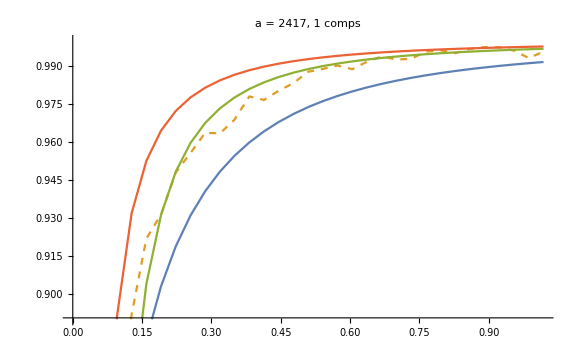
```mathematica
plot10000=-Graphics-;
```

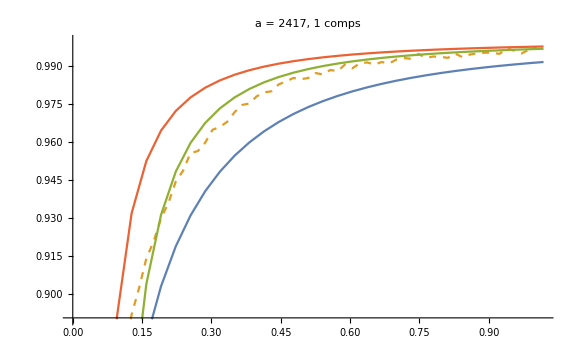
```mathematica
plot20000=-Graphics-;
```

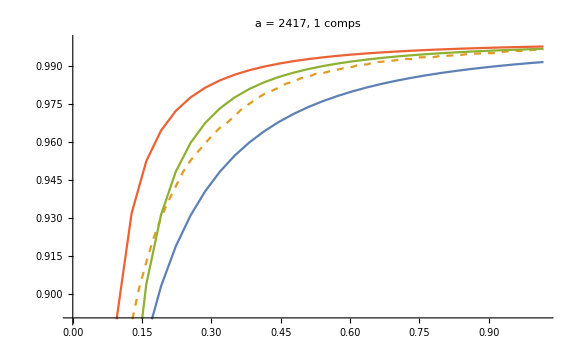
```mathematica
plot1e5=-Graphics-;
```